```mathematica
advmin=5;
advmax=15;
cpmax=300;
cpmin=600;
```

```mathematica
fn[cp_]:=advmin/;cp≥cpmin
fn[cp_]:=advmax/;cp≤cpmax
fn[cp_]:=advmax-(advmax-advmin)*(cp-cpmax)/(cpmin-cpmax);
```

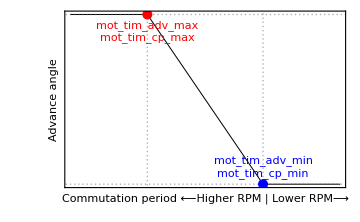

```mathematica
Margin=200;
plot=Plot[fn[cp],{cp,cpmax-Margin,cpmin+Margin},FrameLabel->{"Commutation period\n⟵Higher RPM  |  Lower RPM⟶","Advance angle"},Frame->{True,True,False,False},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->{Black,Thickness[.002]},
FrameTicks->None,
GridLines->{{cpmin,cpmax},{advmin,advmax}},
ImageSize->Medium];
Show[{plot,
Graphics[{Blue,Text["mot_tim_adv_min\nmot_tim_cp_min",{cpmin,advmin+1}]}],
Graphics[{Red,Text["mot_tim_adv_max\nmot_tim_cp_max",{cpmax,advmax-1}]}],
Graphics[{PointSize[.02],Blue,Point[{cpmin,advmin}]}],
Graphics[{PointSize[.02],Red,Point[{cpmax,advmax}]}]},ImageMargins->5]
```